```mathematica
pAdicValuation[x_Integer]:= IntegerExponent[x, p];
pAdicValuation[x_Rational]:=pAdicValuation[Numerator[x]]-pAdicValuation[Denominator[x]];
pAdicValuation[x_List]:=Map[pAdicValuation,x,{2}];
```

```mathematica
(* constructs a basis for M1 whose column vectors can be rescaled to obtain a basis for M2; equivalently, computes a nice matrix for the apartment containing M1 and M2 *)
CommonBasis[M1_,M2_]:=(
newM1=M1;
newM2 = M2;
M = Inverse[M1].M2;
valM = pAdicValuation[M];
d = Dimensions[M1][[1]];
unusedColumns = Range[d];
pivots = {};
NList={M};
For[k=1,k<d,k++,
valM = pAdicValuation[M];
For[l = 1, l ≤Length[pivots],l++,
valM[[pivots[[l]][[1]],pivots[[l]][[2]]]]=Infinity;];
pivot = Position[Transpose[valM],Min[valM],2][[1]];
r = pivot[[2]];
c = pivot[[1]];
pivot ={r,c};
pivots = Append[pivots,pivot];
If[valM[[r,c]]==Infinity,Break[],
R=M;
For[l = 1, l <= d, l ++, 
newM1[[All,r]]=If[l≠r,newM1[[All,r]]+newM1[[All,l]]*M[[l,c]]/M[[r,c]],newM1[[All,r]]];R[[l]] = If[l ≠ r,M[[l]] - M[[l,c]]/M[[r,c]]*M[[r]],M[[r]]]];
M=R;
For[l = 1, l ≤ d, l++,
newM2[[All,l]]=If[l≠c,newM2[[All,l]]  - newM2[[All,c]] * M[[r,l]]/M[[r,c]],newM2[[All,l]]];
R[[All,l]] = If[l≠c, M[[All,l]]-M[[r,l]]/M[[r,c]]*R[[All,c]],R[[All,l]]]];
M=R;
NList = Append[NList,M];];];
rearrangedM2=newM2;
sumOfRowsOfM=Total[M,{2}];
rearrangedM=DiagonalMatrix[sumOfRowsOfM];
For[l = 1, l≤d, l++,
rearrangedM2[[All,l]]=newM1[[All,l]]*sumOfRowsOfM[[l]];];
valuationsOfM = Map[pAdicValuation,sumOfRowsOfM,{1}];
sortedValuationsOfM=Sort[valuationsOfM];
IndexRange=Range[d];
SortedM1=newM1;
SortedM2=rearrangedM2;
sortedMVector=sumOfRowsOfM;
For[l = 1, l≤d, l++,
val = sortedValuationsOfM[[l]];
firstIndex = FirstIndex[valuationsOfM,val];
SortedM1[[All,l]]=newM1[[All,firstIndex]];
SortedM2[[All,l]]=rearrangedM2[[All,firstIndex]];
sortedMVector[[l]]=sumOfRowsOfM[[firstIndex]];
valuationsOfM[[firstIndex]]=Infinity;];
SortedM=DiagonalMatrix[sortedMVector];
(*Print[newM1//MatrixForm,newM2//MatrixForm,M//MatrixForm];*)
matrixList = {SortedM1,SortedM2,SortedM,NList,pivots};
Return[matrixList])
```

```mathematica
(* checks if M1 and M2 correspond to the same lattice class *)
SameClass[M1_,M2_]:=(
divisorMatrix=CommonBasis[M1,M2][[3]];
divisors=Total[divisorMatrix,{1}];
valDivisors=Map[pAdicValuation,divisors,{1}];
Return[Min[valDivisors]==Max[valDivisors]])
```

```mathematica
(* computes the intersection of two lattices *)
LatticeIntersection[M1_,M2_]:=(
divisorMatrix=CommonBasis[M1,M2][[3]];
divisors=Total[divisorMatrix,{2}];
valDivisors=Map[pAdicValuation,divisors,{1}];
d = Dimensions[M1][[1]];
Mat=CommonBasis[M1,M2][[1]];
For[k=1,k<=d,k++,
Mat[[All,k]]=Mat[[All,k]]*p^Max[0,valDivisors[[k]]];];
Return[Mat])
```

```mathematica
(* helper function for computing enveloping membrane 
M a pivot matrix, l the number of leftmost columns which have valuations increment, pivots a list of pivot positions, t the position in pivots of the pivot under consideration *)
MaxIncrementForPivotChange[M_,l_,pivots_, t_]:=(
pivotCol = pivots[[t]][[2]];
If[pivotCol>l,lambdaTemp=Infinity,
d=Dimensions[M][[1]];
pivotVal = pAdicValuation[M[[pivots[[t]][[1]],pivots[[t]][[2]]]]];
lambdaTemp=Infinity;
For[i=t+1,i<d,i++,lambdaTemp=Min[lambdaTemp, pAdicValuation[M[[pivots[[i]][[1]],pivots[[i]][[2]]]]]-pivotVal];];];
Return[lambdaTemp];
)
```

```mathematica
(* helper function for computing enveloping membrane *)FirstIndex[array_,element_]:=(
length = Length[array];
For[index = 1,index≤length,index++,
If[array[[index]]==element,Return[index]];];
Return[-1])
```

```mathematica
(* given three lattices, computes a membrane containing their min-convex hull *)EnvelopingMembraneOfMinConvexTriangle[M1_, M2_, M3_]:= (
d = Dimensions[M1][[1]];
{B2, B3, Delta,NList,pivots} = CommonBasis[M2,M3];
constantList = Total[Delta,{1}];
valuationConstantList = Map[pAdicValuation,constantList,{1}];
commonBasisList={};
For[ell = 1, ell<d, ell++,
cl = valuationConstantList[[ell]];
clplus1=valuationConstantList[[ell+1]];
lambda=cl;
While[lambda < clplus1,
{mat1,mat2,diagmatrix,ListOfNs,pivots}=CommonBasis[M1,LatticeIntersection[p^lambda*B2,B3]];
AppendTo[commonBasisList,mat1];
deltaList={};
For[t=1,t<d,t++,
delta = MaxIncrementForPivotChange[ListOfNs[[t]],ell,pivots,t];
AppendTo[deltaList,delta];
];
minDelta = Min[deltaList];
lambda = lambda + minDelta+1 ;
];
];
lambda = valuationConstantList[[d]];
{mat1,mat2,diagmatrix,ListOfNs,pivots}=CommonBasis[M1,LatticeIntersection[p^lambda*B2,B3]];
AppendTo[commonBasisList,mat1];
Return[Apply[Join,Append[commonBasisList,2]]];
)
```

```mathematica
TropicalRowSum[matrix_]:=(
transpose = Transpose[matrix];
list = {};
numCols = Dimensions[matrix][[2]];
For[i = 1, i <= numCols, i++,
col = transpose[[i]];
AppendTo[list,Min[col]];];
Return[list];
)
```

25

(1/14348907 | 43046721 | 1/2187 | 1/6561 | 1/1594323
1/1594323 | 3486784401 | 1/531441 | 1/19683 | 3
1/1162261467 | 1162261467 | 2187 | 1/14348907 | 59049
19683 | 1/531441 | 1/531441 | 1/129140163 | 1/387420489
1/129140163 | 1/81 | 1/2187 | 1/27 | 3486784401)

(1/3 | 1/6561 | 1/3486784401 | 1/3 | 1/3486784401
59049 | 729 | 1 | 9 | 1/3486784401
1/729 | 6561 | 27 | 243 | 1/1594323
1/14348907 | 6561 | 1/19683 | 9 | 1/2187
531441 | 1/27 | 243 | 1/43046721 | 1/1594323)

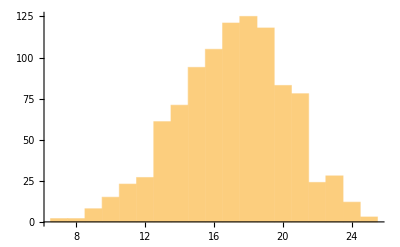

```mathematica
p=3;
columnsList = {};
maxNumColumns=0;
For[forLoopIndex=0,forLoopIndex<1000,forLoopIndex++,
M1 = IdentityMatrix[5];M2 = p^RandomInteger[{-20, 20},{5,5}];M3 = p^RandomInteger[{-20, 20},{5,5}];
If[Det[M2]*Det[M3]≠0,
M = EnvelopingMembraneOfMinConvexTriangle[M1,M2,M3];
M = Transpose[DeleteDuplicates[Transpose[M]]];
numColumns = Dimensions[M][[2]];
If[maxNumColumns <numColumns,
maxNumColumns=numColumns;
maxM2 = M2;
maxM3 = M3;];
AppendTo[columnsList,numColumns];];];
Print[maxNumColumns];
Print[maxM2//MatrixForm];
Print[maxM3//MatrixForm];Histogram[columnsList]
```

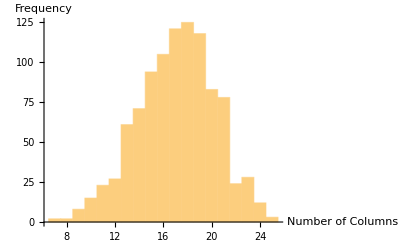

```mathematica
Show[%52,AxesLabel->{HoldForm[Number of Columns],HoldForm[Frequency]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

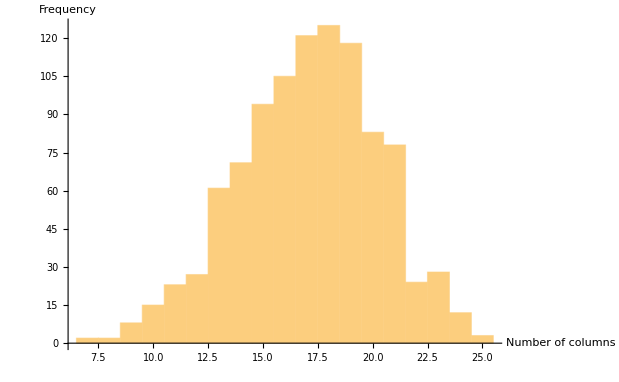

```mathematica
Show[%53,AxesLabel->{HoldForm[HoldForm[Number of columns]],HoldForm[Frequency]},PlotLabel->None]
```

```mathematica
Export["/Users/lzhang/Documents/histogramOfColumns.png",%54,"PNG"]
```

/Users/lzhang/Documents/histogramOfColumns.png

```mathematica
maxM = EnvelopingMembraneOfMinConvexTriangle[M1,maxM2,maxM3];
maxM = Transpose[DeleteDuplicates[Transpose[maxM]]];
Print[pAdicValuation[maxM2]//MatrixForm];
Print[pAdicValuation[maxM3]//MatrixForm];
Print[maxM];
Print[TropicalRowSum[pAdicValuation[Inverse[M1].maxM]]];
Print[TropicalRowSum[pAdicValuation[Inverse[maxM2].maxM]]];
Print[TropicalRowSum[pAdicValuation[Inverse[maxM3].maxM]]];
```

(-15 | 16 | -7 | -8 | -13
-13 | 20 | -12 | -9 | 1
-19 | 19 | 7 | -15 | 10
9 | -12 | -12 | -17 | -18
-17 | -4 | -7 | -3 | 20)

(-1 | -8 | -20 | -1 | -20
10 | 6 | 0 | 2 | -20
-6 | 8 | 3 | 5 | -13
-15 | 8 | -9 | 2 | -7
12 | -3 | 5 | -16 | -13)

{{1,0,0,0,0,475509022218813753828099603369088609705063474116357/158456010007080917047057345843378948148415845990357,1,315309891994896627949476607623721862330592197902880337/9669396964775879543814605539300655639272090947980503246858814,1,10886321689206806682516216719071252382847442746539136737423757852753/179669714766644357367942549809790013637356056793964641156158216747978859505416,1,-1267938029770202418498433944167480941876283314201299/8261741265280504418597195832065068574241754461068415607,29014878551133866797489788269077835416265380687568539458640635/9669396964775879543814605539300655639272090947980503246858814,-137145171567260272565331347829411431106180584166640638434429772171/140410101067625098101282959622565770714234756563056362146818912843447408,539093728440590579602797648776002217950342009296706461559917101722092993805725/179669714766644357367942549809790013637356056793964641156158216747978859505416,3119297802046508287574148566582453677783923818469028503/880982119115721185753136599281147398520966777493891392611910401109,-21407865494485827290226022793324566021050523613371420758555928015917/140410101067625098101282959622565770714234756563056362146818912843447408,75094617656028013590597240268786761/363664920572420244748702848937005439552892,1,-572367874617331950924360042147/2093709646519825956699895312,272748861710359610240300370445769647248387/90916230143105061187175712234251359888223,2779530283277721/261673816513680268606755760,7948342176602998124543410029/1716841910146257284493914155840,81,926510094425799/261673816513680268606755760},{3486784401,1,0,0,0,1,0,0,0,0,0,-422638375815318855366843482866162422532944560494707/8261741265280504418597195832065068574241754461068415607,1,-28569199921322726487442936182392427645302629354282971188609479521/87756313167265686313301849764103606696396722851910226341761820527154630,1,23217764212903576291024445294873884360066851795223897887/880982119115721185753136599281147398520966777493891392611910401109,-4459893675820823497383433729719751218019882121728485313918250176341/87756313167265686313301849764103606696396722851910226341761820527154630,0,0,-25848688778107872156597087/283662057515218257241552,1,13294407179478751643529/261673816513680268606755760,358955047765405187917821/232602887162478970938072640,729,8338590268702551/261673816513680268606755760},{94143178827,1176789708/43584805,6754258536063194430/26594893138513569637,365259442176682118689711823114157/494130171395046145447340622244812323,1,1031377800459237511347133837442158238257519330307607159/158456010007080917047057345843378948148415845990357,94143178827/43584805,1228122623166859663282227642164210881923357588410764547537985/4834698482387939771907302769650327819636045473990251623429407,44314690597791789585510/26594893138513569637,33204880229439541544077229376194839999573867559065325320671027282760440111/44917428691661089341985637452447503409339014198491160289039554186994714876354,374124898007865816385465110963447650700/494130171395046145447340622244812323,144551404903252668692464762642677568471310818631871/8261741265280504418597195832065068574241754461068415607,24005705758763543280230283069876866444040050933489771382927146514/4834698482387939771907302769650327819636045473990251623429407,627102635330413747462691852394940923616354284343544215171859271/175512626334531372626603699528207213392793445703820452683523641054309260,101995288359562189308778073415550344987037842629439366656946417671413933668968403/44917428691661089341985637452447503409339014198491160289039554186994714876354,-95579136075769132281811411264122459368521604666364944127291/880982119115721185753136599281147398520966777493891392611910401109,3070208640587471808752160725448669718269129992512347426655646121741/175512626334531372626603699528207213392793445703820452683523641054309260,1,0,1,0,1,0,1,0},{177147,-177147/435848050,4985318229598146221523/26594893138513569637,1,0,758114970959829494923027364419412255011416569677145973351/158456010007080917047057345843378948148415845990357,694882570797297/435848050,906477313166864014101645843408045862144790507535793359499500948/4834698482387939771907302769650327819636045473990251623429407,32709391182965374852922190/26594893138513569637,1,0,8495094189881774477389887330910320613300364208387027663/8261741265280504418597195832065068574241754461068415607,17622653860704516369781092996123455543874830961323674742294742258585/4834698482387939771907302769650327819636045473990251623429407,1,0,1,0,0,0,0,0,0,0,22876792454961,1},{847288609443,105911075907/435848050,1,0,0,962894349801862356770611895233889390391825942794937519/158456010007080917047057345843378948148415845990357,847288609443/435848050,1,0,0,0,1,0,0,0,-5643854679760340546203624846652143136442613011547588507076436339/880982119115721185753136599281147398520966777493891392611910401109,1,0,0,0,0,4710846704669605542975707592/79778602595634228233767,1,9,-205891132094649/79778602595634228233767}}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{7,12,8,12,10,12,7,13,7,18,7,13,12,18,12,18,13,15,7,15,12,19,13,19}

{20,20,16,15,-8,20,20,16,20,15,20,16,20,15,20,15,16,-8,12,-8,-1,-8,16,-8}

```mathematica
polytopeMatrix = {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{7,12,8,12,10,12,7,13,7,18,7,13,12,18,12,18,13,15,7,15,12,19,13,19}, {20,20,16,15,-8,20,20,16,20,15,20,16,20,15,20,15,16,-8,12,-8,-1,-8,16,-8}};
polytopeMatrixTranspose = Transpose[polytopeMatrix]//DeleteDuplicates//MatrixForm
```

(0 | 7 | 20
0 | 12 | 20
0 | 8 | 16
0 | 12 | 15
0 | 10 | -8
0 | 13 | 16
0 | 18 | 15
0 | 15 | -8
0 | 7 | 12
0 | 12 | -1
0 | 19 | -8)

```mathematica
subMaxM =maxM[[All,{1,2,8,10,24}]];
subMaxM//MatrixForm
CommonBasis[subMaxM,maxM2][[1]]//MatrixForm
```

(1 | 0 | 315309891994896627949476607623721862330592197902880337/9669396964775879543814605539300655639272090947980503246858814 | 10886321689206806682516216719071252382847442746539136737423757852753/179669714766644357367942549809790013637356056793964641156158216747978859505416 | 81
3486784401 | 1 | 0 | 0 | 729
94143178827 | 1176789708/43584805 | 1228122623166859663282227642164210881923357588410764547537985/4834698482387939771907302769650327819636045473990251623429407 | 33204880229439541544077229376194839999573867559065325320671027282760440111/44917428691661089341985637452447503409339014198491160289039554186994714876354 | 1
177147 | -177147/435848050 | 906477313166864014101645843408045862144790507535793359499500948/4834698482387939771907302769650327819636045473990251623429407 | 1 | 22876792454961
847288609443 | 105911075907/435848050 | 1 | 0 | 9)

(81 | 15080864349670289789172028828890759038755116949054042232047139394310888722769356180597245618004591144446340491387721/9374899981690930178233387677038924118394244891868549095589886513452740501935256101957572172388721077996788386010395238519051840 | -200912401133625656137224164814797404981473615128777861827209404892118945326038407543808605385110873743/1716078660689207563080840367893302847823462350225944408180321800750852517120280378388484364897627585513632 | -475509022218813753828099603369088609705063474116357/1657997441048866195564990815454567864063013584115365000556800 | 1
729 | 112250889404565939259538426298895542036404769298573060154151781533072161350502075842851928165564770710819728920963009/9374899981690930178233387677038924118394244891868549095589886513452740501935256101957572172388721077996788386010395238519051840 | -66969590707568589979248424950288509244951852782377797962057730105223605753621374804670933530271540399/1716078660689207563080840367893302847823462350225944408180321800750852517120280378388484364897627585513632 | -158456010007080917047057345843378948148415845990357/1657997441048866195564990815454567864063013584115365000556800 | 3486784401
1 | -462096304133471409073661756957536080412955185297040130195904088274133609547567894628997219527881392430967002906160646437/9374899981690930178233387677038924118394244891868549095589886513452740501935256101957572172388721077996788386010395238519051840 | 22905038861887410410015413983674248999676222094221047168878841589432217364990345335140846803798867947/1716078660689207563080840367893302847823462350225944408180321800750852517120280378388484364897627585513632 | -1031377800459237511347133837442158238257519330307607159/1657997441048866195564990815454567864063013584115365000556800 | 94143178827
22876792454961 | 4259282914299688401440094659270234737633068254557472908683159376739349059762398517308795492721201012920987534613070859516012363/9374899981690930178233387677038924118394244891868549095589886513452740501935256101957572172388721077996788386010395238519051840 | 1346098729963001412672528430958061014112796580429165004180322833902369699770883086689664117968071790245691/1716078660689207563080840367893302847823462350225944408180321800750852517120280378388484364897627585513632 | -758114970959829494923027364419412255011416569677145973351/1657997441048866195564990815454567864063013584115365000556800 | 177147
9 | -27286335655055390259677905737833369288370717728288171184544206263027611350537946324646112804463340825711846754809099496020973/9374899981690930178233387677038924118394244891868549095589886513452740501935256101957572172388721077996788386010395238519051840 | 1309122556607200965521983298232700703156922597482066845895668855541406215957671066260771163924425790301699/1716078660689207563080840367893302847823462350225944408180321800750852517120280378388484364897627585513632 | -962894349801862356770611895233889390391825942794937519/1657997441048866195564990815454567864063013584115365000556800 | 847288609443)

```mathematica
Print[TropicalRowSum[pAdicValuation[Inverse[maxM2].maxM]]];
Print[TropicalRowSum[pAdicValuation[Inverse[maxM3].maxM]]];
```

{7,12,8,12,10,12,7,13,7,18,7,13,12,18,12,18,13,15,7,15,12,19,13,19,18}

{20,20,16,15,-8,20,20,16,20,15,20,16,20,15,20,15,16,-8,12,-8,-1,-8,16,-8,1}

```mathematica
Print[TropicalRowSum[pAdicValuation[Inverse[maxM2].subMaxM]]];
Print[TropicalRowSum[pAdicValuation[Inverse[maxM3].subMaxM]]];
Print[pAdicValuation[Inverse[maxM3].subMaxM]//MatrixForm];Print[pAdicValuation[Inverse[Inverse[maxM3].subMaxM]]//MatrixForm];Print[pAdicValuation[Inverse[maxM2].subMaxM]//MatrixForm];Print[pAdicValuation[Inverse[Inverse[maxM2].subMaxM]]//MatrixForm];Print[pAdicValuation[subMaxM]//MatrixForm];Print[pAdicValuation[Inverse[subMaxM]]//MatrixForm];
```

{7,12,13,18,19}

{20,20,16,15,-8}

(∞ | ∞ | ∞ | 15 | 10
∞ | ∞ | ∞ | ∞ | -8
20 | 20 | 21 | 25 | 4
∞ | ∞ | 16 | 43 | 5
∞ | 20 | 38 | 45 | 18)

(-10 | -8 | -20 | -15 | -20
10 | 6 | ∞ | 2 | -20
12 | -3 | ∞ | -16 | ∞
-15 | 3 | ∞ | ∞ | ∞
∞ | 8 | ∞ | ∞ | ∞)

(20 | 22 | 17 | 37 | 19
7 | 13 | ∞ | ∞ | ∞
26 | 12 | 27 | 27 | ∞
16 | 18 | 13 | 24 | ∞
13 | 18 | 14 | 18 | ∞)

(∞ | -7 | -6 | 4 | 3
∞ | 3 | -12 | -2 | -3
∞ | -4 | -7 | -13 | -7
∞ | -12 | -12 | -17 | -18
-19 | -3 | -5 | -15 | -9)

(0 | ∞ | 1 | 5 | 4
20 | 0 | ∞ | ∞ | 6
23 | 7 | 21 | 9 | 0
11 | 11 | 12 | 0 | 28
25 | 7 | 0 | ∞ | 2)

(0 | 8 | 3 | 5 | 1
20 | 0 | 6 | 15 | 21
22 | 7 | 2 | 11 | 0
11 | 11 | 15 | 0 | 18
20 | 7 | 0 | 9 | 21)